```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
```

### Scanning Parameters

#### masses

```mathematica
mpDPoints = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-1,3}];(*We will scan from 10^-1 GeV to a TeV in increments of 10*) 
mpDPointshigh = mpDPoints[[4;;]];
mpDPointslow = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-3,-2}];(*1 MeV is lowest mass given constraints on ϵ and the fact that we are scanning over meD <= 10^-2 mpD. So at 10 MeV,we run into the red giant cooling bound (since the mass of the lightest species must be above 0.1 MeV)*)


mpDPointshigher = Table["mpD"->10^i 10^12("JpereV")/("c")^2/.SIConstRepl,{i,1,3}];

mpDPointslower = Table["mpD"->10^i 10^6("JpereV")/("c")^2/.SIConstRepl,{i,-2,-1}]; 
(*These values of mpD are ruled out for by stellar cooling bounds, but are the lowest valued meD can be that is consistent with them, hence these values will be used to show capture and evaporation rates for the dark electrons *)
```

```mathematica
meDPoints = Table["meD/mpD"->10^i,{i,-4,-2,2}];(*For each value of mpD we will scan over meD/mpD of 10^-4 and 10^-2*)
```

#### v0

```mathematica
v0Points = {20,220}10^3 ;(*[ms^-1] - average velocity of local aDM for Halo and Disk cases*)
```

#### fD

```mathematica
fDpoints = Table[10^i,{i,-3,-1}];
```

#### κ

```mathematica
κpoints = Table[10^i,{i,-14,-7}];
```

### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

### Debug

#### test runs

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
SaveIt[NotebookDirectory[]<>"FeσDicteallmasses",FeσDicteallmasses]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00114}. NIntegrate obtained 0.0021995 and 2.63835×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00129}. NIntegrate obtained 0.00219805 and 2.35504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00166}. NIntegrate obtained 0.00219441 and 2.71769×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-734.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-853.697] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-992.694] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

40153.9 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

4192.01 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

28426.8 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

20124.6 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

1.70538×10^6 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

5.41386×10^6 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

12697.8 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

1325.63 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

8989.33 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

6363.96 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

539287. 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

1.71201×10^6 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

4015.39 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

419.201 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

2842.68 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

2012.46 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

170538. 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

541386. 6.×10^7

6.×10^7

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicteallmasses.dat

```mathematica
FeσDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointshigh]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictehighmasses",FeσDictehighmasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {34.9086}. NIntegrate obtained 4.40938×10^-16 and 4.75294×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {31.3032}. NIntegrate obtained 2.6296×10^-16 and 4.95046×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {36.549}. NIntegrate obtained 1.91727×10^-16 and 6.06913×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-788.674] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-916.883] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1066.36] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

1269.78 6.×10^7

809807.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

132.563 6.×10^7

327989.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

898.933 6.×10^7

705313.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

636.396 6.×10^7

614302.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

5

53928.7 6.×10^7

891975.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

4

171201. 6.×10^7

992888.

Interpolation::inhr: Requested order is too high; order has been reduced to {3,4}.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

401.539 6.×10^7

510954.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

41.9201 6.×10^7

853950.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

284.268 6.×10^7

445022.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

201.246 6.×10^7

387598.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

5

17053.8 6.×10^7

447046.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

5

54138.6 6.×10^7

894056.

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictehighmasses.dat

#### Plots of dielectrics

```mathematica
AbsoluteTiming@Table[ϵM[u,z,"νi"]/.FeTotalparams[[i]],{i,Length[FeTotalparams]}]
```

{0.0366597,{1+(((0.+1.75116×10^16 ⅈ)+u) (1/z^3(0.+0.103495 ⅈ) (-1/2 (3.06657×10^32-(u-z)^2) (-ArcTan[5.7105×10^-17 (1+u-z)]-ArcTan[5.7105×10^-17 (1-u+z)])+1/2 (3.06657×10^32-(u+z)^2) (-ArcTan[5.7105×10^-17 (1-u-z)]-ArcTan[5.7105×10^-17 (1+u+z)])-8.75581×10^15 (-u+z) Log[(3.06657×10^32+(1+u-z)^2)/(3.06657×10^32+(1-u+z)^2)]+8.75581×10^15 (-u-z) Log[(3.06657×10^32+(1+u+z)^2)/(3.06657×10^32+(1-u-z)^2)])+1/z^3 0.103495 (2 z-1.75116×10^16 (u-z) (-ArcTan[5.7105×10^-17 (1+u-z)]-ArcTan[5.7105×10^-17 (1-u+z)])+1.75116×10^16 (u+z) (-ArcTan[5.7105×10^-17 (1-u-z)]-ArcTan[5.7105×10^-17 (1+u+z)])-1/4 (3.06657×10^32-(u-z)^2) Log[(3.06657×10^32+(1+u-z)^2)/(3.06657×10^32+(1-u+z)^2)]+1/4 (3.06657×10^32-(u+z)^2) Log[(3.06657×10^32+(1+u+z)^2)/(3.06657×10^32+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+4.23008×10^16 ⅈ) z^2 (1/z^3(0.+0.103495 ⅈ) (-1/2 (3.06657×10^32-(u-z)^2) (-ArcTan[5.7105×10^-17 (1+u-z)]-ArcTan[5.7105×10^-17 (1-u+z)])+1/2 (3.06657×10^32-(u+z)^2) (-ArcTan[5.7105×10^-17 (1-u-z)]-ArcTan[5.7105×10^-17 (1+u+z)])-8.75581×10^15 (-u+z) Log[(3.06657×10^32+(1+u-z)^2)/(3.06657×10^32+(1-u+z)^2)]+8.75581×10^15 (-u-z) Log[(3.06657×10^32+(1+u+z)^2)/(3.06657×10^32+(1-u-z)^2)])+1/z^3 0.103495 (2 z-1.75116×10^16 (u-z) (-ArcTan[5.7105×10^-17 (1+u-z)]-ArcTan[5.7105×10^-17 (1-u+z)])+1.75116×10^16 (u+z) (-ArcTan[5.7105×10^-17 (1-u-z)]-ArcTan[5.7105×10^-17 (1+u+z)])-1/4 (3.06657×10^32-(u-z)^2) Log[(3.06657×10^32+(1+u-z)^2)/(3.06657×10^32+(1-u+z)^2)]+1/4 (3.06657×10^32-(u+z)^2) Log[(3.06657×10^32+(1+u+z)^2)/(3.06657×10^32+(1-u-z)^2)]))),1+(((0.+8.99966×10^15 ⅈ)+u) (1/z^3(0.+0.0843793 ⅈ) (-1/2 (8.09939×10^31-(u-z)^2) (-ArcTan[1.11115×10^-16 (1+u-z)]-ArcTan[1.11115×10^-16 (1-u+z)])+1/2 (8.09939×10^31-(u+z)^2) (-ArcTan[1.11115×10^-16 (1-u-z)]-ArcTan[1.11115×10^-16 (1+u+z)])-4.49983×10^15 (-u+z) Log[(8.09939×10^31+(1+u-z)^2)/(8.09939×10^31+(1-u+z)^2)]+4.49983×10^15 (-u-z) Log[(8.09939×10^31+(1+u+z)^2)/(8.09939×10^31+(1-u-z)^2)])+1/z^3 0.0843793 (2 z-8.99966×10^15 (u-z) (-ArcTan[1.11115×10^-16 (1+u-z)]-ArcTan[1.11115×10^-16 (1-u+z)])+8.99966×10^15 (u+z) (-ArcTan[1.11115×10^-16 (1-u-z)]-ArcTan[1.11115×10^-16 (1+u+z)])-1/4 (8.09939×10^31-(u-z)^2) Log[(8.09939×10^31+(1+u-z)^2)/(8.09939×10^31+(1-u+z)^2)]+1/4 (8.09939×10^31-(u+z)^2) Log[(8.09939×10^31+(1+u+z)^2)/(8.09939×10^31+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+2.66643×10^16 ⅈ) z^2 (1/z^3(0.+0.0843793 ⅈ) (-1/2 (8.09939×10^31-(u-z)^2) (-ArcTan[1.11115×10^-16 (1+u-z)]-ArcTan[1.11115×10^-16 (1-u+z)])+1/2 (8.09939×10^31-(u+z)^2) (-ArcTan[1.11115×10^-16 (1-u-z)]-ArcTan[1.11115×10^-16 (1+u+z)])-4.49983×10^15 (-u+z) Log[(8.09939×10^31+(1+u-z)^2)/(8.09939×10^31+(1-u+z)^2)]+4.49983×10^15 (-u-z) Log[(8.09939×10^31+(1+u+z)^2)/(8.09939×10^31+(1-u-z)^2)])+1/z^3 0.0843793 (2 z-8.99966×10^15 (u-z) (-ArcTan[1.11115×10^-16 (1+u-z)]-ArcTan[1.11115×10^-16 (1-u+z)])+8.99966×10^15 (u+z) (-ArcTan[1.11115×10^-16 (1-u-z)]-ArcTan[1.11115×10^-16 (1+u+z)])-1/4 (8.09939×10^31-(u-z)^2) Log[(8.09939×10^31+(1+u-z)^2)/(8.09939×10^31+(1-u+z)^2)]+1/4 (8.09939×10^31-(u+z)^2) Log[(8.09939×10^31+(1+u+z)^2)/(8.09939×10^31+(1-u-z)^2)]))),1+(((0.+2.01886×10^16 ⅈ)+u) (1/z^3(0.+0.0642244 ⅈ) (-1/2 (4.07581×10^32-(u-z)^2) (-ArcTan[4.95328×10^-17 (1+u-z)]-ArcTan[4.95328×10^-17 (1-u+z)])+1/2 (4.07581×10^32-(u+z)^2) (-ArcTan[4.95328×10^-17 (1-u-z)]-ArcTan[4.95328×10^-17 (1+u+z)])-1.00943×10^16 (-u+z) Log[(4.07581×10^32+(1+u-z)^2)/(4.07581×10^32+(1-u+z)^2)]+1.00943×10^16 (-u-z) Log[(4.07581×10^32+(1+u+z)^2)/(4.07581×10^32+(1-u-z)^2)])+1/z^3 0.0642244 (2 z-2.01886×10^16 (u-z) (-ArcTan[4.95328×10^-17 (1+u-z)]-ArcTan[4.95328×10^-17 (1-u+z)])+2.01886×10^16 (u+z) (-ArcTan[4.95328×10^-17 (1-u-z)]-ArcTan[4.95328×10^-17 (1+u+z)])-1/4 (4.07581×10^32-(u-z)^2) Log[(4.07581×10^32+(1+u-z)^2)/(4.07581×10^32+(1-u+z)^2)]+1/4 (4.07581×10^32-(u+z)^2) Log[(4.07581×10^32+(1+u+z)^2)/(4.07581×10^32+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+7.85863×10^16 ⅈ) z^2 (1/z^3(0.+0.0642244 ⅈ) (-1/2 (4.07581×10^32-(u-z)^2) (-ArcTan[4.95328×10^-17 (1+u-z)]-ArcTan[4.95328×10^-17 (1-u+z)])+1/2 (4.07581×10^32-(u+z)^2) (-ArcTan[4.95328×10^-17 (1-u-z)]-ArcTan[4.95328×10^-17 (1+u+z)])-1.00943×10^16 (-u+z) Log[(4.07581×10^32+(1+u-z)^2)/(4.07581×10^32+(1-u+z)^2)]+1.00943×10^16 (-u-z) Log[(4.07581×10^32+(1+u+z)^2)/(4.07581×10^32+(1-u-z)^2)])+1/z^3 0.0642244 (2 z-2.01886×10^16 (u-z) (-ArcTan[4.95328×10^-17 (1+u-z)]-ArcTan[4.95328×10^-17 (1-u+z)])+2.01886×10^16 (u+z) (-ArcTan[4.95328×10^-17 (1-u-z)]-ArcTan[4.95328×10^-17 (1+u+z)])-1/4 (4.07581×10^32-(u-z)^2) Log[(4.07581×10^32+(1+u-z)^2)/(4.07581×10^32+(1-u+z)^2)]+1/4 (4.07581×10^32-(u+z)^2) Log[(4.07581×10^32+(1+u+z)^2)/(4.07581×10^32+(1-u-z)^2)]))),1+(((0.+9.30837×10^16 ⅈ)+u) (1/z^3(0.+0.03308 ⅈ) (-1/2 (8.66457×10^33-(u-z)^2) (-ArcTan[1.0743×10^-17 (1+u-z)]-ArcTan[1.0743×10^-17 (1-u+z)])+1/2 (8.66457×10^33-(u+z)^2) (-ArcTan[1.0743×10^-17 (1-u-z)]-ArcTan[1.0743×10^-17 (1+u+z)])-4.65418×10^16 (-u+z) Log[(8.66457×10^33+(1+u-z)^2)/(8.66457×10^33+(1-u+z)^2)]+4.65418×10^16 (-u-z) Log[(8.66457×10^33+(1+u+z)^2)/(8.66457×10^33+(1-u-z)^2)])+1/z^3 0.03308 (2 z-9.30837×10^16 (u-z) (-ArcTan[1.0743×10^-17 (1+u-z)]-ArcTan[1.0743×10^-17 (1-u+z)])+9.30837×10^16 (u+z) (-ArcTan[1.0743×10^-17 (1-u-z)]-ArcTan[1.0743×10^-17 (1+u+z)])-1/4 (8.66457×10^33-(u-z)^2) Log[(8.66457×10^33+(1+u-z)^2)/(8.66457×10^33+(1-u+z)^2)]+1/4 (8.66457×10^33-(u+z)^2) Log[(8.66457×10^33+(1+u+z)^2)/(8.66457×10^33+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+7.03474×10^17 ⅈ) z^2 (1/z^3(0.+0.03308 ⅈ) (-1/2 (8.66457×10^33-(u-z)^2) (-ArcTan[1.0743×10^-17 (1+u-z)]-ArcTan[1.0743×10^-17 (1-u+z)])+1/2 (8.66457×10^33-(u+z)^2) (-ArcTan[1.0743×10^-17 (1-u-z)]-ArcTan[1.0743×10^-17 (1+u+z)])-4.65418×10^16 (-u+z) Log[(8.66457×10^33+(1+u-z)^2)/(8.66457×10^33+(1-u+z)^2)]+4.65418×10^16 (-u-z) Log[(8.66457×10^33+(1+u+z)^2)/(8.66457×10^33+(1-u-z)^2)])+1/z^3 0.03308 (2 z-9.30837×10^16 (u-z) (-ArcTan[1.0743×10^-17 (1+u-z)]-ArcTan[1.0743×10^-17 (1-u+z)])+9.30837×10^16 (u+z) (-ArcTan[1.0743×10^-17 (1-u-z)]-ArcTan[1.0743×10^-17 (1+u+z)])-1/4 (8.66457×10^33-(u-z)^2) Log[(8.66457×10^33+(1+u-z)^2)/(8.66457×10^33+(1-u+z)^2)]+1/4 (8.66457×10^33-(u+z)^2) Log[(8.66457×10^33+(1+u+z)^2)/(8.66457×10^33+(1-u-z)^2)]))),1+(((0.+7.408×10^17 ⅈ)+u) (1/z^3(0.+0.00652082 ⅈ) (-1/2 (5.48784×10^35-(u-z)^2) (-ArcTan[1.34989×10^-18 (1+u-z)]-ArcTan[1.34989×10^-18 (1-u+z)])+1/2 (5.48784×10^35-(u+z)^2) (-ArcTan[1.34989×10^-18 (1-u-z)]-ArcTan[1.34989×10^-18 (1+u+z)])-3.704×10^17 (-u+z) Log[(5.48784×10^35+(1+u-z)^2)/(5.48784×10^35+(1-u+z)^2)]+3.704×10^17 (-u-z) Log[(5.48784×10^35+(1+u+z)^2)/(5.48784×10^35+(1-u-z)^2)])+1/z^3 0.00652082 (2 z-7.408×10^17 (u-z) (-ArcTan[1.34989×10^-18 (1+u-z)]-ArcTan[1.34989×10^-18 (1-u+z)])+7.408×10^17 (u+z) (-ArcTan[1.34989×10^-18 (1-u-z)]-ArcTan[1.34989×10^-18 (1+u+z)])-1/4 (5.48784×10^35-(u-z)^2) Log[(5.48784×10^35+(1+u-z)^2)/(5.48784×10^35+(1-u+z)^2)]+1/4 (5.48784×10^35-(u+z)^2) Log[(5.48784×10^35+(1+u+z)^2)/(5.48784×10^35+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+2.84013×10^19 ⅈ) z^2 (1/z^3(0.+0.00652082 ⅈ) (-1/2 (5.48784×10^35-(u-z)^2) (-ArcTan[1.34989×10^-18 (1+u-z)]-ArcTan[1.34989×10^-18 (1-u+z)])+1/2 (5.48784×10^35-(u+z)^2) (-ArcTan[1.34989×10^-18 (1-u-z)]-ArcTan[1.34989×10^-18 (1+u+z)])-3.704×10^17 (-u+z) Log[(5.48784×10^35+(1+u-z)^2)/(5.48784×10^35+(1-u+z)^2)]+3.704×10^17 (-u-z) Log[(5.48784×10^35+(1+u+z)^2)/(5.48784×10^35+(1-u-z)^2)])+1/z^3 0.00652082 (2 z-7.408×10^17 (u-z) (-ArcTan[1.34989×10^-18 (1+u-z)]-ArcTan[1.34989×10^-18 (1-u+z)])+7.408×10^17 (u+z) (-ArcTan[1.34989×10^-18 (1-u-z)]-ArcTan[1.34989×10^-18 (1+u+z)])-1/4 (5.48784×10^35-(u-z)^2) Log[(5.48784×10^35+(1+u-z)^2)/(5.48784×10^35+(1-u+z)^2)]+1/4 (5.48784×10^35-(u+z)^2) Log[(5.48784×10^35+(1+u+z)^2)/(5.48784×10^35+(1-u-z)^2)]))),1+(((0.+5.21962×10^18 ⅈ)+u) (1/z^3(0.+0.00142216 ⅈ) (-1/2 (2.72444×10^37-(u-z)^2) (-ArcTan[1.91585×10^-19 (1+u-z)]-ArcTan[1.91585×10^-19 (1-u+z)])+1/2 (2.72444×10^37-(u+z)^2) (-ArcTan[1.91585×10^-19 (1-u-z)]-ArcTan[1.91585×10^-19 (1+u+z)])-2.60981×10^18 (-u+z) Log[(2.72444×10^37+(1+u-z)^2)/(2.72444×10^37+(1-u+z)^2)]+2.60981×10^18 (-u-z) Log[(2.72444×10^37+(1+u+z)^2)/(2.72444×10^37+(1-u-z)^2)])+1/z^3 0.00142216 (2 z-5.21962×10^18 (u-z) (-ArcTan[1.91585×10^-19 (1+u-z)]-ArcTan[1.91585×10^-19 (1-u+z)])+5.21962×10^18 (u+z) (-ArcTan[1.91585×10^-19 (1-u-z)]-ArcTan[1.91585×10^-19 (1+u+z)])-1/4 (2.72444×10^37-(u-z)^2) Log[(2.72444×10^37+(1+u-z)^2)/(2.72444×10^37+(1-u+z)^2)]+1/4 (2.72444×10^37-(u+z)^2) Log[(2.72444×10^37+(1+u+z)^2)/(2.72444×10^37+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+9.17551×10^20 ⅈ) z^2 (1/z^3(0.+0.00142216 ⅈ) (-1/2 (2.72444×10^37-(u-z)^2) (-ArcTan[1.91585×10^-19 (1+u-z)]-ArcTan[1.91585×10^-19 (1-u+z)])+1/2 (2.72444×10^37-(u+z)^2) (-ArcTan[1.91585×10^-19 (1-u-z)]-ArcTan[1.91585×10^-19 (1+u+z)])-2.60981×10^18 (-u+z) Log[(2.72444×10^37+(1+u-z)^2)/(2.72444×10^37+(1-u+z)^2)]+2.60981×10^18 (-u-z) Log[(2.72444×10^37+(1+u+z)^2)/(2.72444×10^37+(1-u-z)^2)])+1/z^3 0.00142216 (2 z-5.21962×10^18 (u-z) (-ArcTan[1.91585×10^-19 (1+u-z)]-ArcTan[1.91585×10^-19 (1-u+z)])+5.21962×10^18 (u+z) (-ArcTan[1.91585×10^-19 (1-u-z)]-ArcTan[1.91585×10^-19 (1+u+z)])-1/4 (2.72444×10^37-(u-z)^2) Log[(2.72444×10^37+(1+u-z)^2)/(2.72444×10^37+(1-u+z)^2)]+1/4 (2.72444×10^37-(u+z)^2) Log[(2.72444×10^37+(1+u+z)^2)/(2.72444×10^37+(1-u-z)^2)])))}}

```mathematica
uνFit[z_] := ("νi"/(2 "vF" "qF" z)) (*u ν*)
zb[sign_,ω_,mχ_,vχ_,params_]:= ((mχ vχ + <|"+"->1,"-"->(-1)|>[[sign]] Sqrt[2 mχ (1/2 mχ vχ^2 - ω "ℏ")])/(2"qF""ℏ")) /.params (*section 10.2 of notes*)
kb[sign_,ω_,mχ_,vχ_,params_]:= 2 ("qF"/.params)zb[sign,ω,mχ,vχ,params]
Thetab[ω_,k_,mχ_,vχ_,params_]:=HeavisideTheta[kb["+",ω,mχ,vχ,params]-k]HeavisideTheta[k-kb["-",ω,mχ,vχ,params]]HeavisideTheta[1/2 mχ vχ^2 - ω "ℏ"/.params]
TotalThetab[ω_,k_,mχ_,vχ_,params_]:=Sum[Thetab[ω,k,mχ,vχ,params[[i]]],{i,Length[params]}]
```

```mathematica
Clear[StructureFunction]
StructureFunction[ω_,k_,mχ_,vχ_,params_,n_:4,truncate_:True,cut_:4]:=Sum[(2 ("e")^2/(vχ "ℏ" (2 π)^2 "ϵ0") (1+HeavisideTheta[cut - "β" "ℏ" ω](1/(1-E^(- "β" "ℏ" ω))-1))/.params[[i]])(z^n/z /.z->k/(2 "qF")/.params[[i]])If[truncate,Thetab[ω,k,mχ,vχ,params[[i]]],1]Im[-("Ai"/.params[[i]]) / Dielectrics`ϵMNum[("ℏ"ω)/(2"EF"z)/.z->k/(2 "qF")/.params[[i]], k/(2 "qF")/.params[[i]], uνFit[z]/.z-> k/(2 "qF")/. params[[i]], params[[i]]]],{i,Length[params]}](*taking κ = 1*)
```

```mathematica
Clear[StructureFunctionDebug]
StructureFunctionDebug[ω_,k_,mχ_,vχ_,params_, cut_:4]:=N[Sum[Im[-("Ai"/.params[[i]]) / Dielectrics`ϵMNum[("ℏ"ω)/(2"EF"z)/.z->k/(2 "qF")/.params[[i]], k/(2 "qF")/.params[[i]], uνFit[z]/.z-> k/(2 "qF")/. params[[i]], params[[i]]]],{i,Length[params]}],30]
```

```mathematica
AbsoluteTiming@StructureFunction[10^16,10^10,"m"/.SIConstRepl,10^5,FeTotalparams]
```

{0.008336,1.65789}

```mathematica
Thetab[w 10^12,k 10^10,"m"/.SIConstRepl,10^5,FeTotalparams[[1]]]
```

HeavisideTheta[10000000000 k-9.47867×10^33 (9.11×10^-26-1.34981×10^-15 √(4.555×10^-21-1.055×10^-22 w))] HeavisideTheta[-10000000000 k+9.47867×10^33 (9.11×10^-26+1.34981×10^-15 √(4.555×10^-21-1.055×10^-22 w))]

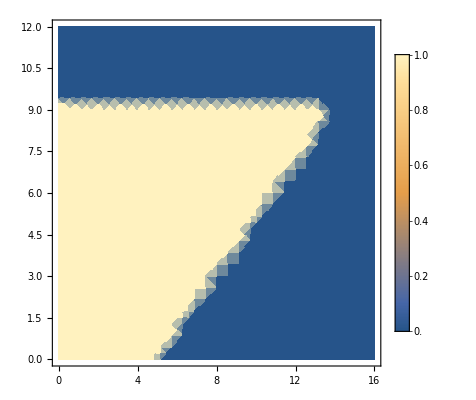

```mathematica
DensityPlot[Thetab[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams[[1]]],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

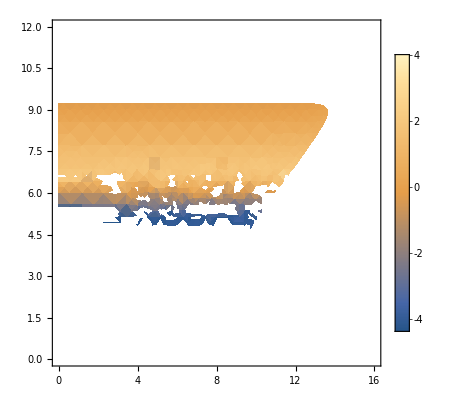

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

So the structure function becomes negative,

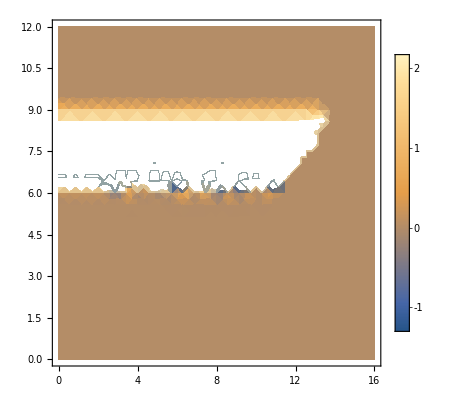

```mathematica
DensityPlot[StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

```mathematica
"qF"/.FeTotalparams
```

{1.45392×10^10,1.78329×10^10,2.34292×10^10,4.54874×10^10,2.30757×10^11,1.05805×10^12}

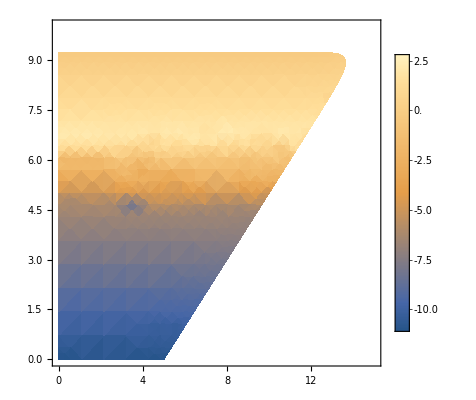

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic]
```

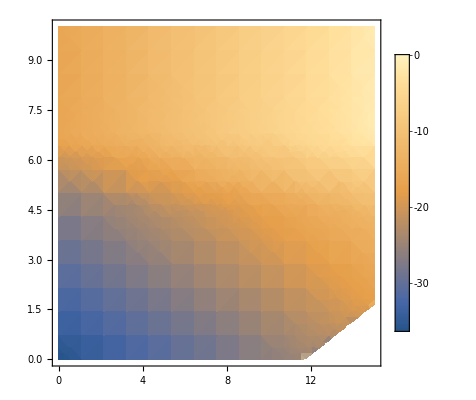

```mathematica
DensityPlot[Log10@Abs@StructureFunctionDebug[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic]
```

Here is just the imaginary part of the polarization with no kinematic restrictions, note the small scaling, it seems like there may be some differences and sums of large or small numbers where we see the grainy regions in the middle of the plot

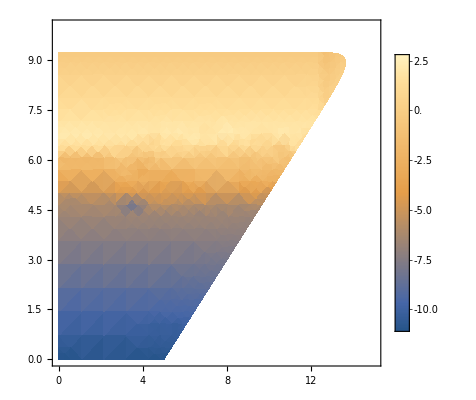

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams,0.1],{w,0,15},{k,0,10},PlotLegends->Automatic]
```

This is the same as two plots above just changing when we truncate the FD distribution (approximate as 1) - controlled by the “cut” parameter in the function. Note the top right of the plot, there is a discontinuity which reduces the value of the function slightly. This also tells us that our default cut at 4 doesn’t significantly affect the value of the function

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams,100],{w,0,15},{k,0,10},PlotLegends->Automatic]
```

-Graphics-

Weaker cut still, is identical to the plot with cut = 4

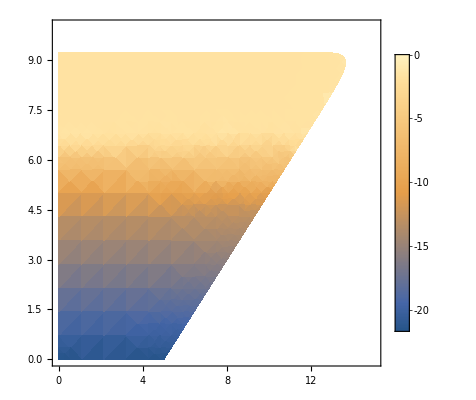

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic](*1st moment*)
```

Graininess reduced when we use the first moment instead of the 0th (ie. 1/small number may be responsible for the graniness). Let’s see how far we can smooth it out by working with higher moments and dividing them out after interpolating.

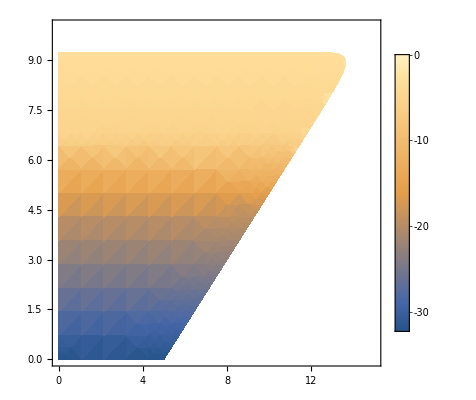

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic](*2nd moment*)
```

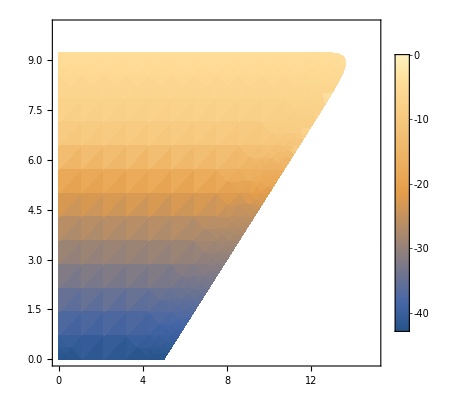

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams,3],{w,0,15},{k,0,10},PlotLegends->Automatic](*3rd moment*)
```

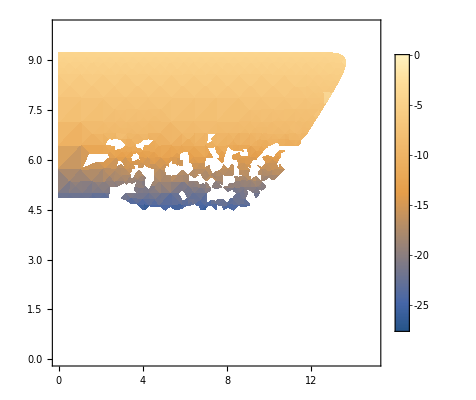

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic](*3rd moment no abs*)
```

So the graininess / negative values are not due to the large prefactor, they just help the precision to keep it homogeneous. This seems to support the difference of large numbers hypothesis.

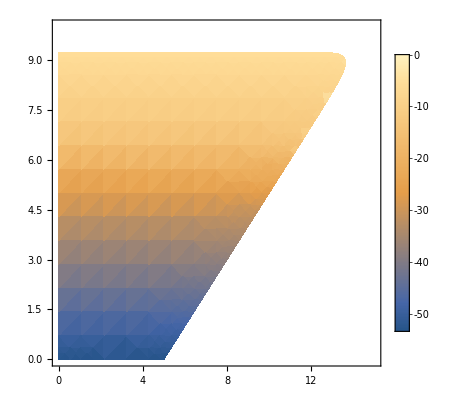

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic](*4th moment*)
```

Ooh la la so smooth. Let’s use this!

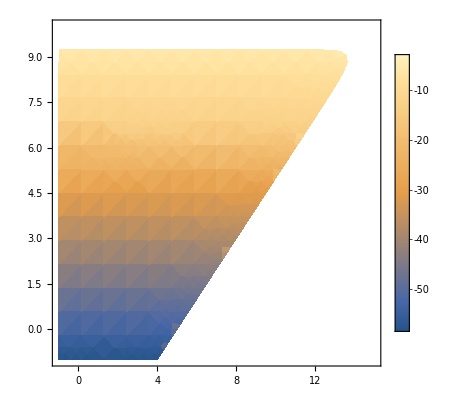

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,-1,15},{k,-1,10},PlotLegends->Automatic](*4th moment*)
```

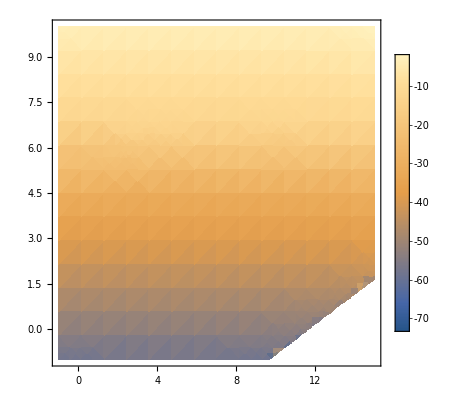

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams,4,False],{w,-1,15},{k,-1,10},PlotLegends->Automatic](*4th moment no truncation*)
```

It would be easier to use the unkinematically restricted version of the function for the interpolation since we will be using it for a range of velocities. So what is going on in the bottom right?

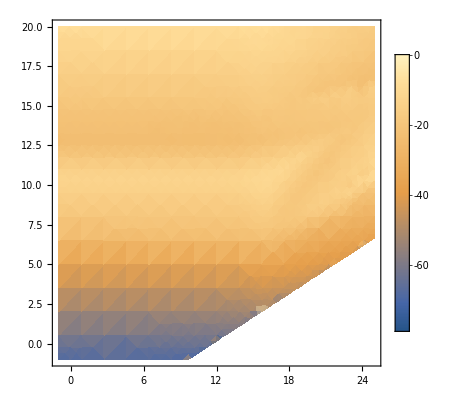

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False],{w,-1,25},{k,-1,20},PlotLegends->Automatic,PlotRange->All](*4th moment no truncation*)
```

```mathematica
Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False]/.{w->22.5,k->2.5}
```

General::munfl: Exp[-8.3303×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Indeterminate

So it looks like this may be part of the reason we are having slow down issues. Intedeterminate values may be throwing things off. Let’s look in the text files as david suggested.

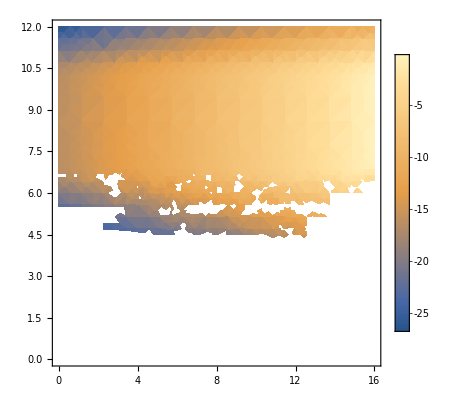

```mathematica
DensityPlot[Log10@StructureFunctionDebug[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

```mathematica
"ℏ"("qF")/("m")/.FeTotalparams
"vF"/.FeTotalparams
```

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

```mathematica
StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams]/.w->1/.k->1
```

-1.09188×10^-10

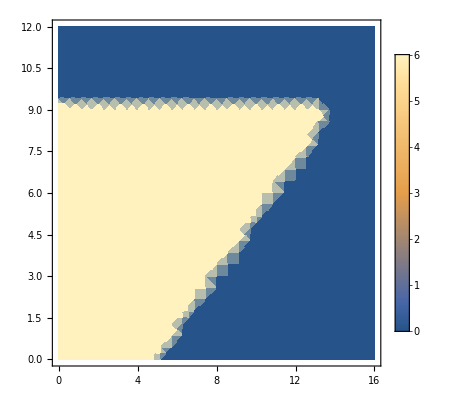

```mathematica
DensityPlot[TotalThetab[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

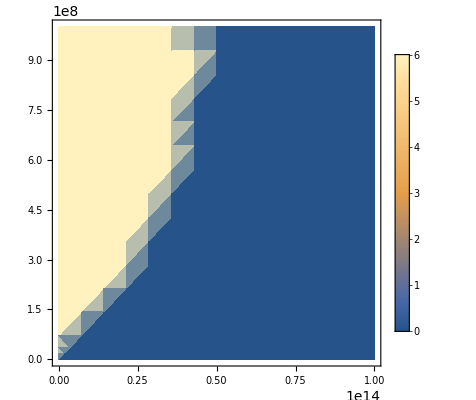

```mathematica
DensityPlot[TotalThetab[w,k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,10^14},{k,0,10^9},PlotLegends->Automatic]
```

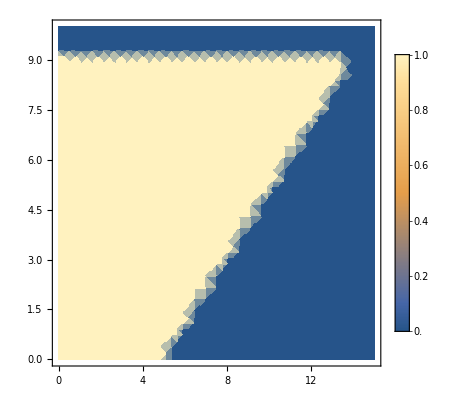

```mathematica
DensityPlot[HeavisideTheta[((10^k v-("ℏ"(10^k)^2)/(2 m))/.{m->"m"/.SIConstRepl,v->10^5}/.SIConstRepl)-10^w],{w,0,15},{k,0,10},PlotLegends->Automatic](*This is equivalent to θb*)
```

Need to interpolate, so we need to use this simpler form to change the boundaries to a rectangular grid

#### Investigate z=1 pole

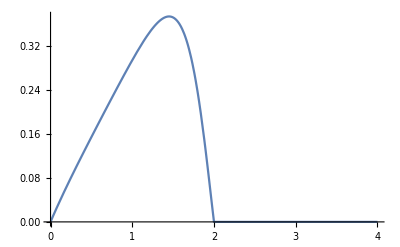

```mathematica
Plot[Im[-1/uzLinDielectric[u,1]/."χ"->1],{u,0,4}]
```

```mathematica
Plot[Im[-1/ϵM[u,1]/."χ"->1],{u,0,4}]
```

-Graphics-

```mathematica
Im[-1/ϵM[u,1,2]/."χ"->1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

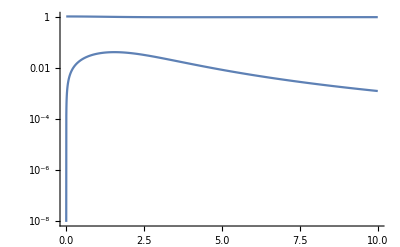

```mathematica
LogPlot[ϵRPAC[u,1,2]/."χ"->1,{u,0,10}]
```

Just complex part looks okay. Non-zero and non-singular away from 0

```mathematica
ϵRPA0[z]-1
%/.z->1
```

(χ^2 (1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z)))/z^2

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

```mathematica
uzLinDielectric[0,z]
```

1+(χ^2 (1/2+((1-z^2) Log[Abs[(1+z)/(1-z)]])/(4 z)+ⅈ (Piecewise[{{0, z<1}, {(π (1-z^2))/(8 z), Abs[z]<1<z}, {0, True}}])))/z^2

```mathematica
Refine[uzLinDielectric[0,z],Assumptions->z>0]
```

1+(χ^2 (1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z)))/z^2

```mathematica
Limit[ϵRPA0[z]-1,z->0]
```

χ^2 ∞

```mathematica
Series[ϵRPA0[z]-1,{z,1,1}]//Simplify
```

Log[(2+(z-1)+O[z-1]^2)/Abs[1-z]] (-1/2 χ^2 (z-1)+O[z-1]^2)+(χ^2/2-χ^2 (z-1)+O[z-1]^2)

```mathematica
Series[Log[1/x],{x,0,2}]
```

Log[1/x]+O[x]^3

```mathematica
ϵM[1,1.000000000000001,1]
```

1-(0.0120658-0.222051 ⅈ) χ^2

```mathematica
Limit[ϵM[u,z,uν],z->1]
```

1+(χ^2 (8+4 (-1+u) uν (ArcTan[(2-u)/uν]+ArcTan[u/uν])+4 (1+u) uν (ArcTan[u/uν]-ArcTan[(2+u)/uν])+(-2 u+u^2-uν^2) Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-(2 u+u^2-uν^2) Log[((2+u)^2+uν^2)/(u^2+uν^2)]+2 ⅈ (-((-2 u+u^2-uν^2) (ArcTan[(2-u)/uν]+ArcTan[u/uν]))+(-2 u-u^2+uν^2) (ArcTan[u/uν]-ArcTan[(2+u)/uν])+(-1+u) uν Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-(1+u) uν Log[((2+u)^2+uν^2)/(u^2+uν^2)])))/(2 (8+2 (-2+u+ⅈ uν) uν ArcTan[(2-u)/uν]+4 (u+ⅈ uν) uν ArcTan[u/uν]-4 uν ArcTan[(2+u)/uν]-2 u uν ArcTan[(2+u)/uν]-2 ⅈ uν^2 ArcTan[(2+u)/uν]-2 ⅈ uν Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]+ⅈ u uν Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-uν^2 Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-2 ⅈ uν Log[((2+u)^2+uν^2)/(u^2+uν^2)]-ⅈ u uν Log[((2+u)^2+uν^2)/(u^2+uν^2)]+uν^2 Log[((2+u)^2+uν^2)/(u^2+uν^2)]))

So it has a well defined limit at the branch point.